```mathematica
DEList={{12845,12863,12915,12950,12965,12972,13150,13154,13216,13604,13734,13752,13800,13806,14134,14630,14673,14686,14695,14791,14820,14841,14853,14882,14893,14936,14960,14994,15144,15251,15433,15491,15621,15704,15774,15803,15876,15935,15956,16044,16053,16066,16072,16075,16081,16081,16125,16131,16133,16154,16201,16222,16301,16315,16336,16342,16356,16413,16424,16430,16444,16446,16461,16463,16470,16561,16601,16660,16663,16664,16672,16710,16714,16720,16725,17023,17060,17071,17275,17311,17445,17673,17792,17810,17812,18022,18104},{199,1070,245,1073,329,103,1547,1775,2614,2543,2046,1637,2135,2543,914,2625,2228,1832,738,1771,835,1828,352,711,2669,2419,2299,1714,269,2092,141,1896,2720,1825,1436,2166,2528,2361,561,915,2724,2817,1134,737,1843,2745,2489,2696,2680,1810,2759,2371,1639,2458,1828,1901,1548,2680,1978,1898,2501,2488,2416,2479,1819,1244,1213,568,338,2221,569,286,1445,1820,190,729,1541,2634,1726,433,542,1445,2228,1541,241,2474,733}};
index=2

GPSDay=DEList[[1,index]]
Event=DEList[[2,index]]

BiasData=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/dataStream_",ToString[GPSDay],"_",ToString[Event],".txt"],"Table"];
Template=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/signalTemplate",ToString[GPSDay],"-",ToString[Event],".out"],"Table"];
Eij=Import[StringJoin["/Users/nv/Downloads/results/oc3Eij/oc3Eij",ToString[GPSDay],".out"],"Table"];
info=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/info",ToString[GPSDay],".out"],"Table"][[5,All]];
Einv=Inverse[Eij];
Flattemplate=Flatten[Template];
h=Flattemplate.Einv.Flatten[BiasData]/(Transpose[Flattemplate].Einv.Flattemplate);
V=Einv.Flatten[BiasData]/Sqrt[Transpose[Flattemplate].Einv.Flattemplate];
SNR=Flattemplate.V
```

2

12863

1070

6.79166

```mathematica
Data=Partition[V,61];
sortedPairs=SortBy[Transpose[{Template, Data,info}],First[Position[Template,1]]];
sorted1=sortedPairs[[All,1]];
sorted2=sortedPairs[[All,2]];
sorted3=sortedPairs[[All,3]];
```

```mathematica
DW=Reverse[sorted2];
```

```mathematica
Length[Template]
S=Sign[SNR]*Reverse[sorted1];
```

20

```mathematica
Finish=First[Position[sorted1,1]][[2]]
```

33

```mathematica
Start=Last[Position[sorted1,1]][[2]]
```

29

```mathematica
spacing=0.16;
```

```mathematica
TileCount=Total[Total[Abs[Template]]]
```

26

```mathematica
Max2=SNR/TileCount;
Min2=-1.0*Max2;
```

```mathematica
Max[DW]
```

2.41118

```mathematica
NumClocks=Length[Template]
JW=61;
NewJW=Finish-Start+1
NewSize=NumClocks*NewJW
DoF=NewSize-1
ETrimmed=ConstantArray[0,{NewSize,NewSize}];
```

20

5

100

99

```mathematica
For[a=0,a<NumClocks,a++,
For[s=1,s<=NewJW,s++,
For[b=0,b<NumClocks,b++,
For[t=1,t<=NewJW,t++,
ETrimmed[[NewJW*b+t,NewJW*a+s]]=Eij[[JW*b+t-1+Start,JW*a+s-1+Start]];
];
];
];
];
```

```mathematica
ETrimmedinv=Inverse[ETrimmed];
DmS=Flatten[Transpose[Transpose[BiasData][[Start;;Finish]]]-h*Transpose[Transpose[Template][[Start;;Finish]]]];
Chi2Mini=Transpose[DmS].ETrimmedinv.DmS
Chi2=Transpose[Flatten[BiasData-h*Template]].Einv.Flatten[BiasData-h*Template]
```

161.532

1141.44

```mathematica
dist=ChiSquareDistribution[DoF];
Chi2MiniThres=Quantile[dist,1-5.802891933*10^-7]
```

183.068

```mathematica
dist=ChiSquareDistribution[JW*NumClocks];
Chi2Thres=Quantile[dist,1-5.802891933*10^-7]
```

1475.45

## Putting it together

```mathematica
spacing=0.4;
```

```mathematica
fontsize=32
```

32

```mathematica
BackFill[array1_,array2_,array3_,max2_,min2_]:=Module[{rows,cols,grid1,grid2,grid3,grid4,white0,clockLabels},{rows,cols}=Dimensions[array1];grid1=Table[Style[Rectangle[{j-1+spacing,rows-i+spacing},{j,rows-i+1}],EdgeForm[{Thickness[0.000],Opacity[1],White}],ColorData["TemperatureMap"][Rescale[array2[[i,j]],{min2,max2}]]],{i,1,rows},{j,1,cols} ];
grid2=Table[Style[Rectangle[{j-1+spacing-0.15,rows-i+spacing-0.15},{j+0.15,rows-i+1+0.15}],EdgeForm[{Thickness[0.00],If[array1[[i,j]]==0, White, ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]]}],FaceForm[{If[array1[[i,j]]==0, White, ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]]}]],{i,1,rows},{j,1,cols}];
grid4=Table[Style[Rectangle[{j-1+spacing-0.03,rows-i+spacing-0.03},{j+0.03,rows-i+1+0.03}],EdgeForm[{Thickness[0.00],If[array1[[i,j]]==0, White, ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]]}],FaceForm[{ White}]],{i,1,rows},{j,1,cols}];
grid3=Table[Style[Rectangle[{j-1+spacing+0.1,rows-i+spacing+0.1},{j-0.1,rows-i+1-0.1}],EdgeForm[{Thickness[0.015],Opacity[0],If[array1[[i,j]]==0,White,ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]]}],FaceForm[{Opacity[If[Abs[array2[[i,j]]]>Abs[Max2],1,0]],Black}]],{i,1,rows},{j,1,cols}];
white0=Table[Style[Rectangle[{j-1+spacing-0.2,rows-i+spacing-0.1},{j+0.1,rows-i+1+0.1}],EdgeForm[{Thickness[0.015],Opacity[0],If[array1[[i,j]]==0,White,ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]]}],FaceForm[{Opacity[1],White}]],{i,1,rows},{j,1,Start-1}];
clockLabels=Table[Text[Style[array3[[i]],Black,24],{Start-1.1,rows-i+0.7},{1,0} ],{i,1,rows}];
Graphics[{grid2,grid4,grid1,grid3,white0,clockLabels},PlotRange->{{Start-1.5,Finish+0.15},{0,rows+0.2}},AspectRatio->(rows+0.15)/(Finish-Start+1.5+0.15),ImageSize->(Finish-Start+1.5+0.15)*100,PlotLabel->Column[{Style[StringJoin["Event Number: ",ToString[index]],fontsize,Black],Style[StringJoin["GPS Day: ",ToString[GPSDay]],fontsize,Black],Style[StringJoin["GPS Time: ",ToString[Floor[30*Event/3600]],":",ToString[Floor[(30*Event/60)-60*Floor[30*Event/3600]]],":",ToString[Round[60*(Event*0.5-Floor[Event*0.5])]]],fontsize,Black],Style[StringJoin["v_⊥ = ",ToString[Round[27.33*61/(Finish-Start)]]," km/s"],fontsize,Black],Style[StringJoin["χ^2 = ",ToString[NumberForm[Chi2/Chi2Thres,2]]," | ",ToString[NumberForm[Chi2Mini/Chi2MiniThres,2]]],fontsize,Black]},Alignment->Center],Frame->True,FrameTicks->{{None,None},{None,None}}]]
```

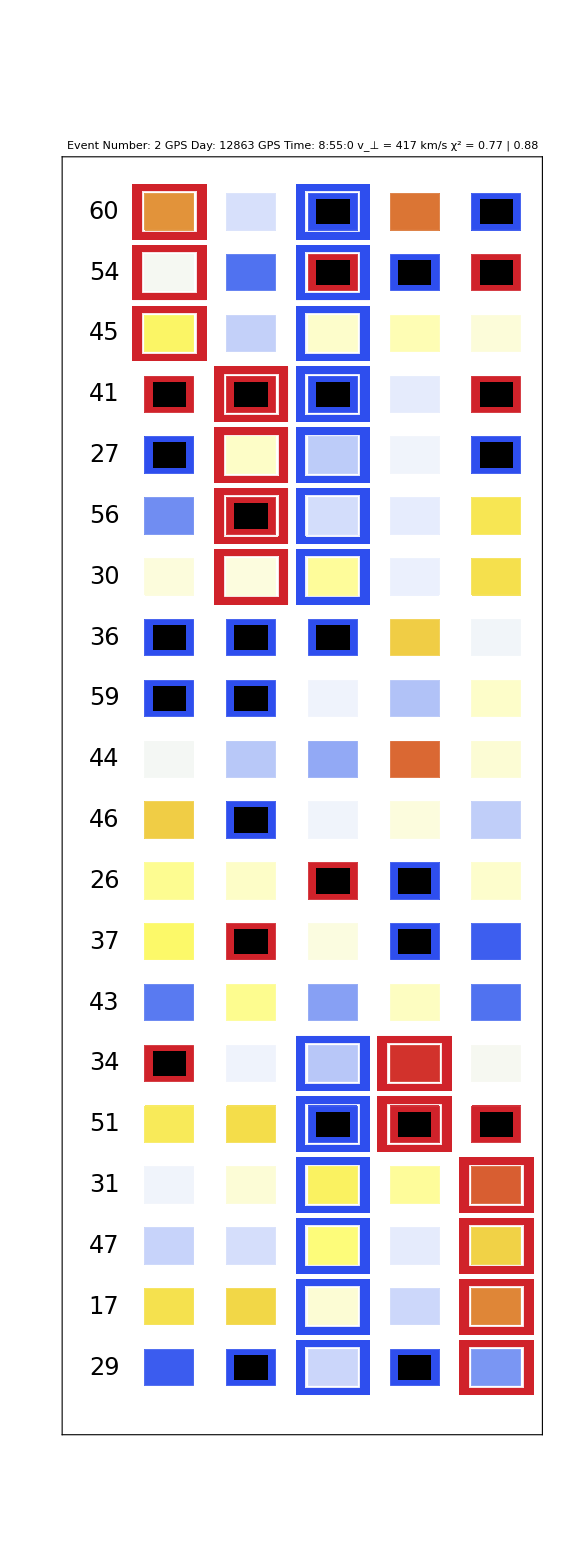

```mathematica
bf=BackFill[S,DW,sorted3,Max2,Min2]
```

```mathematica
Export[StringJoin["/Users/nv/Downloads/results/EinOutput2/Ein",ToString[GPSDay],"_",ToString[Event],".pdf"],bf]
```

/Users/nv/Downloads/results/EinOutput2/Ein12863_1070.pdf

```mathematica
bfr=Rasterize[bf]
```

-Graphics-

```mathematica
L=BarLegend[{"TemperatureMap",{-Abs[h],Abs[h]}},LegendMarkerSize->600]
```

```mathematica
GraphicsRow[{bfr,bfr},ImageSize->1200]
```

-Graphics-

```mathematica
Clocks=Grid[Transpose[{sorted3}],Spacings->{0,1.54}];
```

```mathematica
Export[StringJoin["/Users/nv/Downloads/results/EinOutput2/Ein",ToString[GPSDay],"_",ToString[Event],".pdf"],bf]
(*
Export[StringJoin["/Users/nv/Downloads/results/EinOutput/",ToString[GPSDay],"/Einvtileplot_",ToString[GPSDay],"_",ToString[Event],".PDF"],MainChart]
Export[StringJoin["/Users/nv/Downloads/results/EinOutput/",ToString[GPSDay],"/Einvclocks_",ToString[GPSDay],"_",ToString[Event],".PDF"],Clocks]
Export[StringJoin["/Users/nv/Downloads/results/EinOutput/",ToString[GPSDay],"/Einvlegend_",ToString[GPSDay],"_",ToString[Event],".PDF"],L]
```

/Users/nv/Downloads/results/EinOutput2/Ein12863_1070.pdf

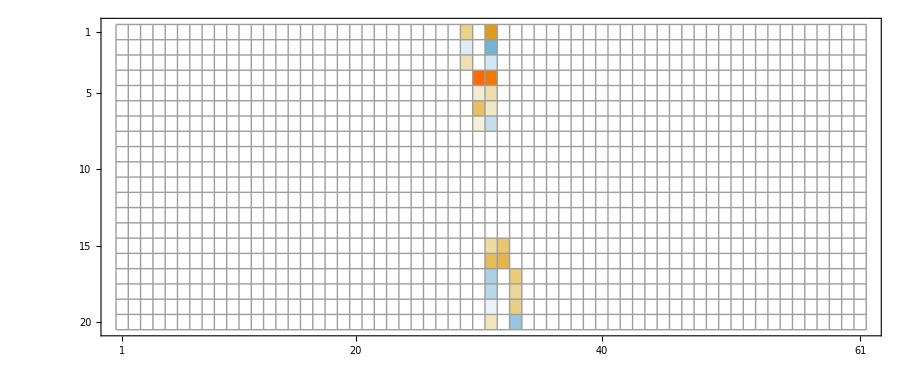

```mathematica
ContributionChart=MatrixPlot[Partition[Flatten[S]*Flatten[DW],61],Mesh->All]
```

```mathematica
Export[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/Einvcontribution_",ToString[GPSDay],"_",ToString[Event],".PDF"],ContributionChart]
```

/Users/nv/Downloads/results/12863/Einvcontribution_12863_1070.PDF

```mathematica
SNRContribution=Partition[Flatten[S]*Flatten[DW],61]//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.191005 | 0. | 0.848632 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0203814 | 0. | -0.409812 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0955446 | 0. | -0.0277238 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.41118 | 1.96708 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0309719 | 0.10617 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.283108 | 0.0835346 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00930693 | -0.0616207 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.111335 | 0.252752 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.296833 | 0.327576 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.100381 | 0. | 0.228648 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0794329 | 0. | 0.139089 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0187518 | 0. | 0.202142 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0929366 | 0. | -0.168073 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Max2
```

0.261218

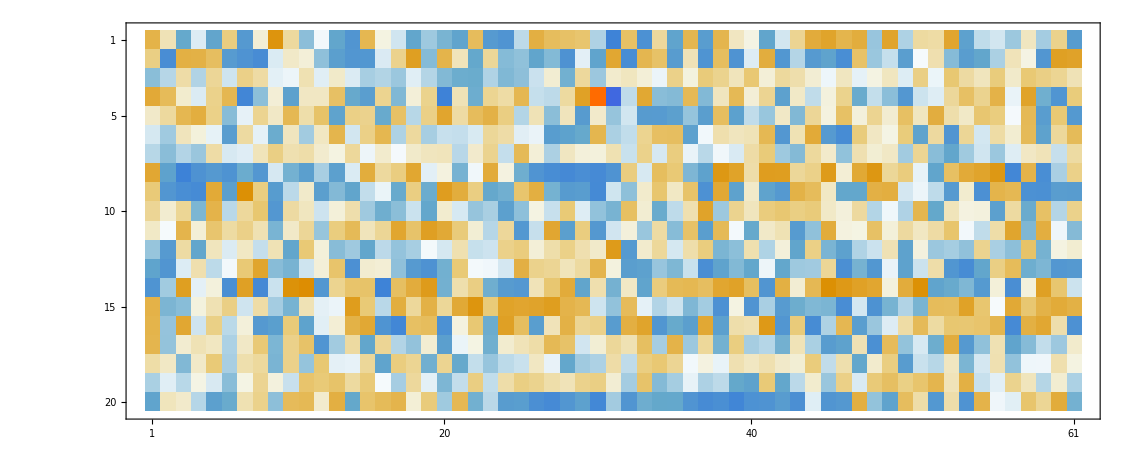

```mathematica
MatrixPlot[DW]
```

```mathematica
Total[Flatten[S]*Flatten[DW]]
```

6.79166

```mathematica
Max[DW]
Min[DW]
```

2.41118

-1.96708

```mathematica
Mean[Mean[Abs[DW]]]
```

0.17664

```mathematica
Max[Max[DW],Abs[Min[DW]]]
```

2.41118

```mathematica
newArray=Transpose[Transpose[DW][[Start;;Finish]]];
```

```mathematica
newArray//MatrixForm
```

(0.191005 | -0.0778855 | -0.848632 | 0.215636 | -0.443812
-0.0203814 | -0.215809 | 0.409812 | -0.537068 | 0.280962
0.0955446 | -0.100569 | 0.0277238 | 0.0467472 | 0.014444
0.48394 | 2.41118 | -1.96708 | -0.058058 | 0.405256
-0.306138 | 0.0309719 | -0.10617 | -0.0390713 | -0.305021
-0.178971 | 0.283108 | -0.0835346 | -0.0556764 | 0.117477
0.0112495 | 0.00930693 | 0.0616207 | -0.0490775 | 0.125059
-0.49643 | -0.595816 | -0.398917 | 0.142843 | -0.0342654
-0.293961 | -0.612871 | -0.0405221 | -0.117618 | 0.029188
-0.0239635 | -0.11085 | -0.146554 | 0.223283 | 0.0191816
0.143295 | -0.343728 | -0.0391454 | 0.0103692 | -0.103293
0.0664911 | 0.0313692 | 0.591189 | -0.322675 | 0.026329
0.0911032 | 0.291596 | 0.00760941 | -0.276464 | -0.240843
-0.205359 | 0.0674697 | -0.156603 | 0.036429 | -0.215826
0.268306 | -0.0416186 | -0.111335 | 0.252752 | -0.0185482
0.110715 | 0.128841 | -0.296833 | 0.327576 | 0.4422
-0.0391002 | 0.0169036 | 0.100381 | 0.0615055 | 0.228648
-0.0969166 | -0.0809987 | 0.0794329 | -0.0579372 | 0.139089
0.124034 | 0.13515 | 0.0187518 | -0.0918412 | 0.202142
-0.243671 | -0.678551 | -0.0929366 | -0.373546 | -0.168073)

```mathematica
Max[Max[newArray],Abs[Min[newArray]]]
```

2.41118

```mathematica
Mean[Abs[Flatten[newArray]]]
```

0.221958

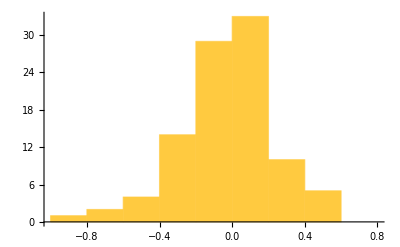

```mathematica
Histogram[Flatten[newArray]]
```